## Phase A

```mathematica
astrologerSuccess={3,10,9,7,16,17,13,20,4,1};expected={6,12,13,9,14,12.66666667,12.66666667,17,5,1.333333333};
```

```mathematica
data=N[astrologerSuccess/expected]
```

{0.5,0.833333,0.692308,0.777778,1.14286,1.34211,1.02632,1.17647,0.8,0.75}

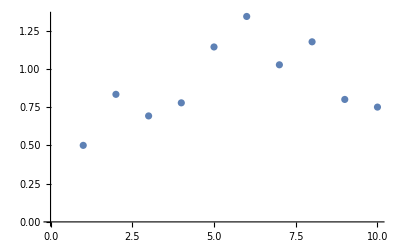

```mathematica
ListPlot[data]
```

```mathematica
lmfA=LinearModelFit[data,x,x]
```

FittedModel[0.724705+0.0326203 x]

```mathematica
Normal[lmfA]
```

0.724705+0.0326203 x

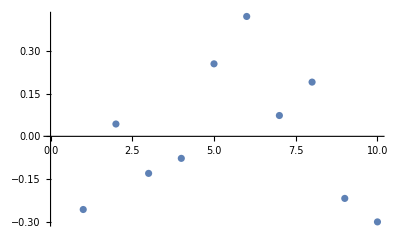

```mathematica
ListPlot[lmfA["FitResiduals"]]
```

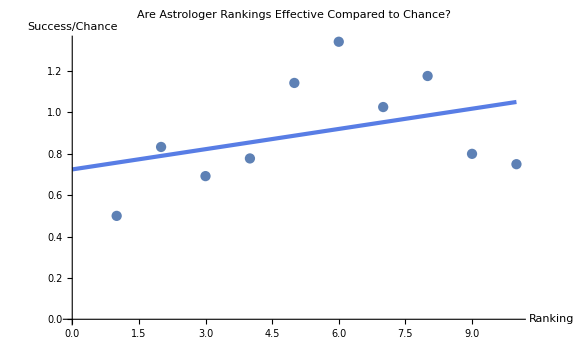

```mathematica
Show[ListPlot[data,PlotLabel->"Are Astrologer Rankings Effective Compared to Chance?",AxesLabel->{"Ranking","Success/Chance"}],Plot[lmf[x],{x,0,10},PlotTheme->"Business"],ImageSize->Large ]
```

```mathematica
lmfA["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.724705 | 0.173139 | 4.18569 | 0.0030557
x | 0.0326203 | 0.0279038 | 1.16903 | 0.276045

```mathematica
lmfA["ParameterConfidenceIntervals"]
```

{{0.325447,1.12396},{-0.031726,0.0969666}}

```mathematica
lmfA["RSquared"]
```

0.145903

```mathematica
lmfA["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.0877867 | 0.0877867 | 1.36662 | 0.276045
Error | 8 | 0.513891 | 0.0642364 |  | 
Total | 9 | 0.601678 |  |  |

Check Cook distances to identify highly influential points :

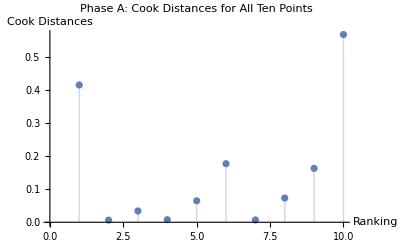

```mathematica
ListPlot[cdA=lmfA["CookDistances"],PlotRange->{0,All},Filling->0,AxesLabel->{"Ranking","Cook Distances"},PlotLabel->"Phase A: Cook Distances for All Ten Points",ImageSize->"Large"]
```

```mathematica
Position[cdA,_?(#>.5&)]
```

{{10}}

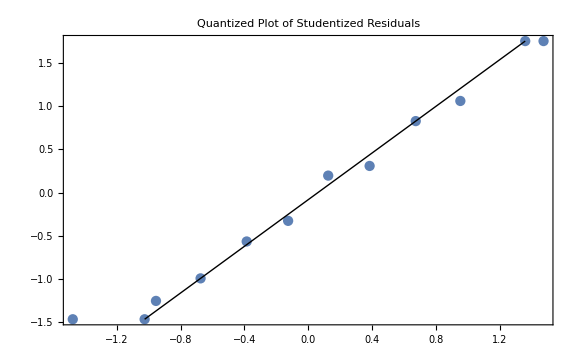

```mathematica
QuantilePlot[lmfA["StandardizedResiduals"],Table[InverseCDF[NormalDistribution[],q],{q,1/100,99/100,1/50}],PlotLabel->"Quantized Plot of Studentized Residuals",ImageSize->Large]
```

Use DFFITS values to assess the influence of each point on the fitted values :

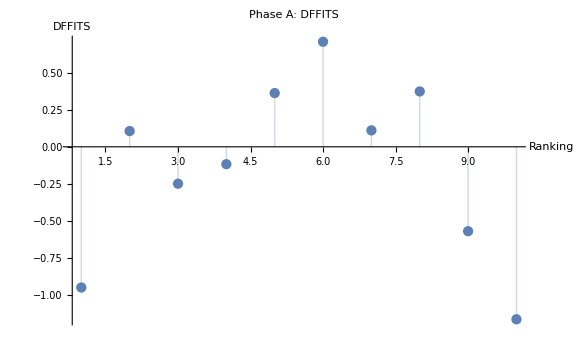

```mathematica
ListPlot[lmfA["FitDifferences"],PlotRange->All,Filling->0,"PlotLabel"->"Phase A: DFFITS",AxesLabel->{"Ranking","DFFITS"},ImageSize->Large]
```

Use DFBETAS values to assess the influence of each point on each estimated parameter :

```mathematica
N[2/Sqrt[10]]
```

0.632456

```mathematica
dfbetasA=Transpose[lmfA["BetaDifferences"]]
```

{{-0.94802,0.104226,-0.232384,-0.0964876,0.22102,0.216049,-4.00511×10^-18,-0.0872096,0.223478,0.581074},{0.802133,-0.0823081,0.163853,0.0544264,-0.0623362,0.121868,0.0514793,0.245964,-0.441205,-0.98331}}

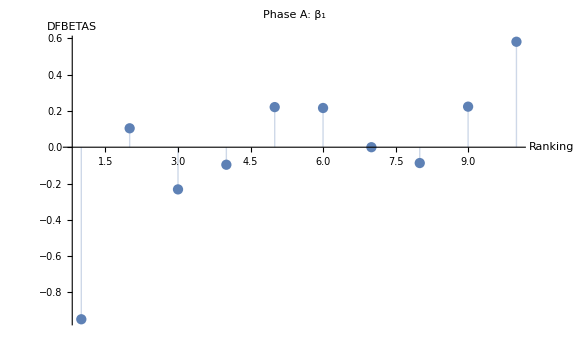
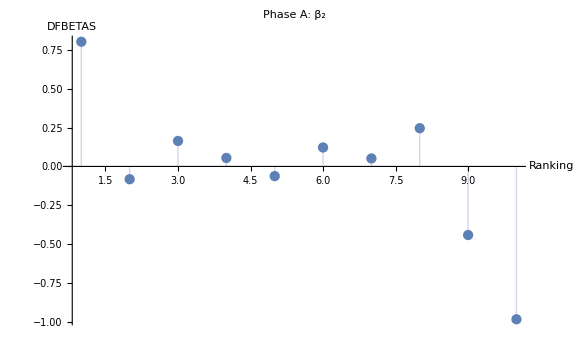

```mathematica
MapThread[ListPlot[#1,PlotRange->All,Filling->0,PlotLabel->"Phase A: "<>#2,ImageSize->Large,AxesLabel->{"Ranking","DFBETAS"}]&,{Transpose[lmf["BetaDifferences"]],{"β_1","β_2"(*,"β_3"*)}}]//Row
```

## Phase B

```mathematica
astrologerSuccess={3,10,9,7,16,17,13,20,4(*,1*)};expected={6,12,13,9,14,12.66666667,12.66666667,17,5(*,1.333333333*)};
```

```mathematica
data=N[astrologerSuccess/expected]
```

{0.5,0.833333,0.692308,0.777778,1.14286,1.34211,1.02632,1.17647,0.8}

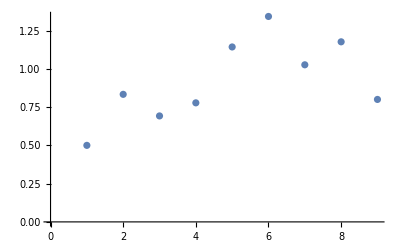

```mathematica
ListPlot[data]
```

```mathematica
lmfB=LinearModelFit[data,x,x]
```

FittedModel[0.632761+0.0576959 x]

```mathematica
Normal[lmfB]
```

0.632761+0.0576959 x

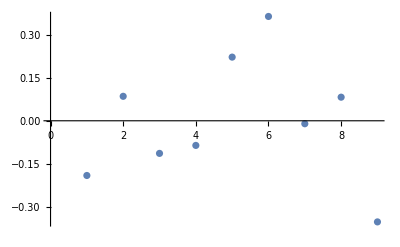

```mathematica
ListPlot[lmfB["FitResiduals"]]
```

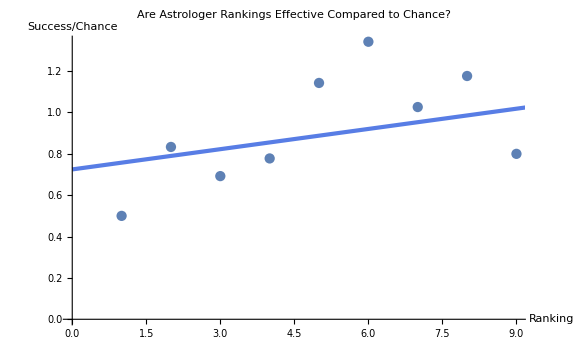

```mathematica
Show[ListPlot[data,PlotLabel->"Are Astrologer Rankings Effective Compared to Chance?",AxesLabel->{"Ranking","Success/Chance"}],Plot[lmfB[x],{x,0,10},PlotTheme->"Business"],ImageSize->Large ]
```

```mathematica
lmfB["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.632761 | 0.168273 | 3.76032 | 0.00707189
x | 0.0576959 | 0.0299029 | 1.92944 | 0.0950004

```mathematica
lmfB["ParameterConfidenceIntervals"]
```

{{0.234859,1.03066},{-0.0130132,0.128405}}

```mathematica
lmfB["RSquared"]
```

0.347182

```mathematica
lmfB["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.199729 | 0.199729 | 3.72274 | 0.0950004
Error | 7 | 0.375557 | 0.0536511 |  | 
Total | 8 | 0.575287 |  |  |

Check Cook distances to identify highly influential points :

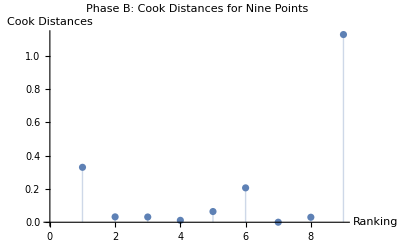

```mathematica
ListPlot[cdB=lmfB["CookDistances"],PlotRange->{0,All},Filling->0,AxesLabel->{"Ranking","Cook Distances"},PlotLabel->"Phase B: Cook Distances for Nine Points",ImageSize->"Large"]
```

```mathematica
Position[cdB,_?(#>.5&)]
```

{{9}}

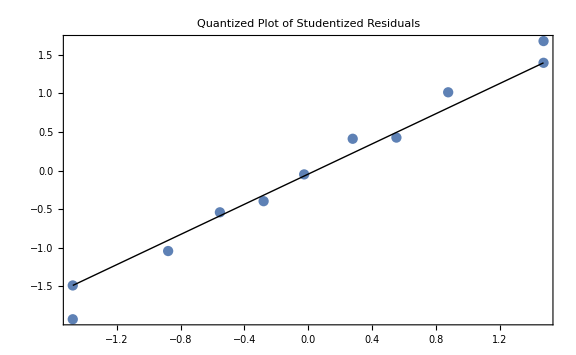

```mathematica
QuantilePlot[lmfB["StandardizedResiduals"],Table[InverseCDF[NormalDistribution[],q],{q,1/100,99/100,1/50}],PlotLabel->"Quantized Plot of Studentized Residuals",ImageSize->Large]
```

Use DFFITS values to assess the influence of each point on the fitted values :

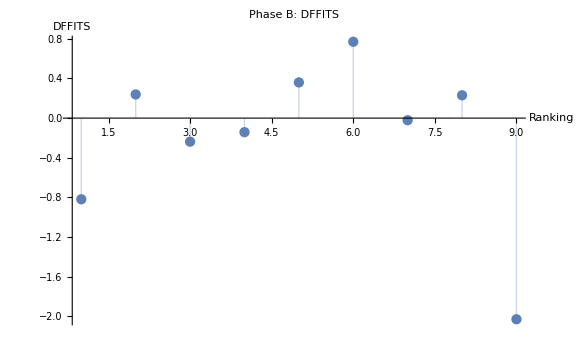

```mathematica
ListPlot[lmfB["FitDifferences"],PlotRange->All,Filling->0,"PlotLabel"->"Phase B: DFFITS",AxesLabel->{"Ranking","DFFITS"},ImageSize->Large]
```

Use DFBETAS values to assess the influence of each point on each estimated parameter :

```mathematica
N[2/Sqrt[9]]
```

0.666667

```mathematica
dfbetasB=Transpose[lmfB["BetaDifferences"]]
```

{{-0.814351,0.232095,-0.215593,-0.106398,0.165037,0.0823324,0.00383596,-0.0860024,1.00929},{0.687391,-0.180841,0.145585,0.0513201,-1.37421×10^-17,0.277986,-0.0129517,0.174227,-1.70389}}

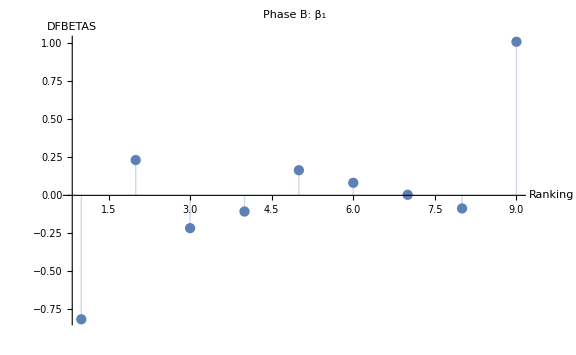
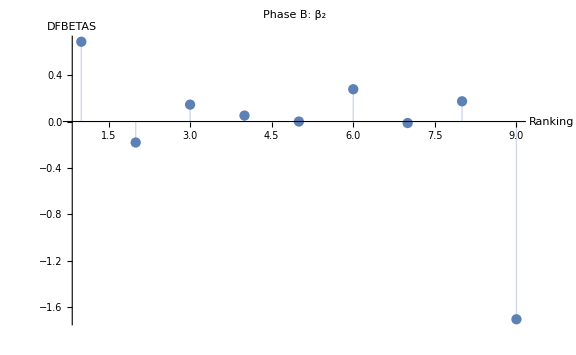

```mathematica
MapThread[ListPlot[#1,PlotRange->All,Filling->0,PlotLabel->"Phase B: "<>#2,ImageSize->Large,AxesLabel->{"Ranking","DFBETAS"}]&,{Transpose[lmfB["BetaDifferences"]],{"β_1","β_2"(*,"β_3"*)}}]//Row
```

## Phase C

```mathematica
astrologerSuccess={3,10,9,7,16,17,13,20(*,4*)(*,1*)};expected={6,12,13,9,14,12.66666667,12.66666667,17(*,5*)(*,1.333333333*)};
```

```mathematica
data=N[astrologerSuccess/expected]
```

{0.5,0.833333,0.692308,0.777778,1.14286,1.34211,1.02632,1.17647}

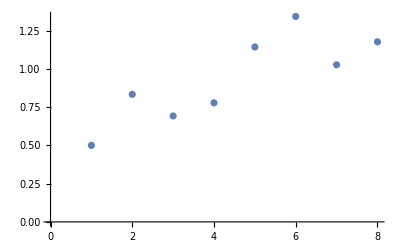

```mathematica
ListPlot[data]
```

```mathematica
lmfC=LinearModelFit[data,x,x]
```

FittedModel[0.507038+0.0954128 x]

```mathematica
Normal[lmfC]
```

0.507038+0.0954128 x

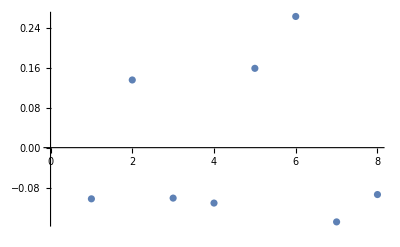

```mathematica
ListPlot[lmfC["FitResiduals"]]
```

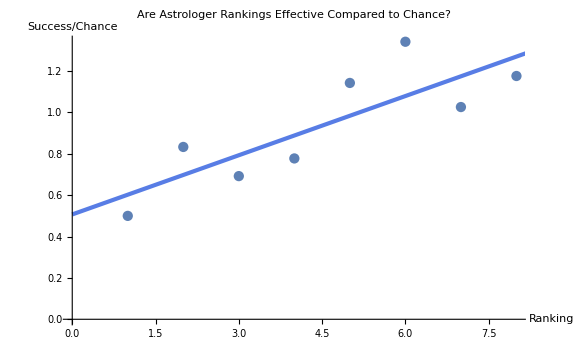

```mathematica
Show[ListPlot[data,PlotLabel->"Are Astrologer Rankings Effective Compared to Chance?",AxesLabel->{"Ranking","Success/Chance"}],Plot[lmfC[x],{x,0,10},PlotTheme->"Business"],ImageSize->Large ]
```

```mathematica
lmfC["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.507038 | 0.133603 | 3.7951 | 0.00901931
x | 0.0954128 | 0.0264574 | 3.60628 | 0.0112811

```mathematica
lmfC["ParameterConfidenceIntervals"]
```

{{0.180123,0.833953},{0.030674,0.160152}}

```mathematica
lmfC["RSquared"]
```

0.684298

```mathematica
lmfC["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 0.382352 | 0.382352 | 13.0053 | 0.0112811
Error | 6 | 0.176398 | 0.0293997 |  | 
Total | 7 | 0.55875 |  |  |

Check Cook distances to identify highly influential points :

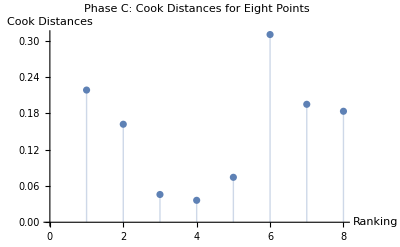

```mathematica
ListPlot[cdC=lmfC["CookDistances"],PlotRange->{0,All},Filling->0,AxesLabel->{"Ranking","Cook Distances"},PlotLabel->"Phase C: Cook Distances for Eight Points",ImageSize->"Large"]
```

```mathematica
Position[cdC,_?(#>.5&)]
```

{}

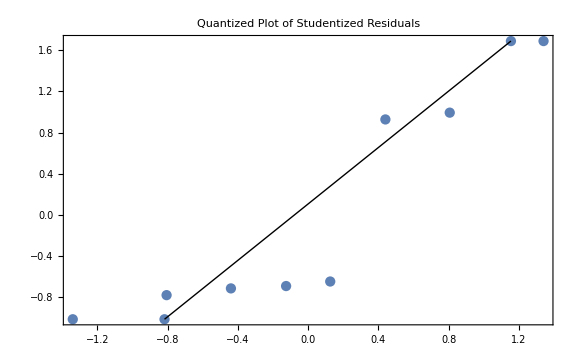

```mathematica
QuantilePlot[lmfC["StandardizedResiduals"],Table[InverseCDF[NormalDistribution[],q],{q,1/100,99/100,1/50}],PlotLabel->"Quantized Plot of Studentized Residuals",ImageSize->Large]
```

Use DFFITS values to assess the influence of each point on the fitted values :

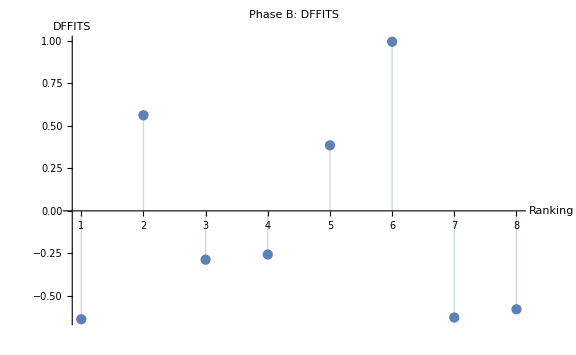

```mathematica
ListPlot[lmfC["FitDifferences"],PlotRange->All,Filling->0,"PlotLabel"->"Phase B: DFFITS",AxesLabel->{"Ranking","DFFITS"},ImageSize->Large]
```

Use DFBETAS values to assess the influence of each point on each estimated parameter :

```mathematica
N[2/Sqrt[8]]
```

0.707107

```mathematica
dfbetasC=Transpose[lmfC["BetaDifferences"]]
```

{{-0.633177,0.540997,-0.248877,-0.162369,0.0975326,-0.107752,0.219579,0.287464},{0.532898,-0.413924,0.157096,0.0546615,0.0820859,0.544121,-0.462009,-0.483874}}

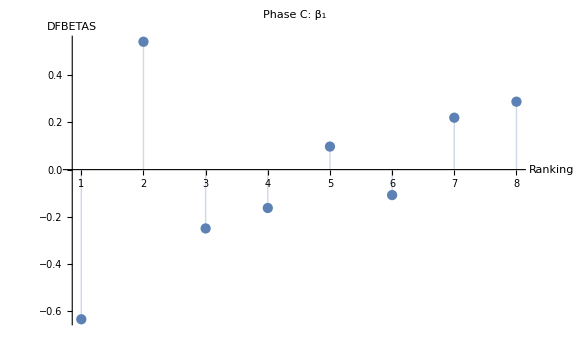
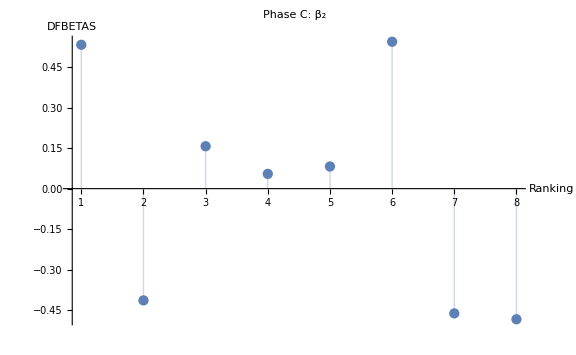

```mathematica
MapThread[ListPlot[#1,PlotRange->All,Filling->0,PlotLabel->"Phase C: "<>#2,ImageSize->Large,AxesLabel->{"Ranking","DFBETAS"}]&,{Transpose[lmfC["BetaDifferences"]],{"β_1","β_2"(*,"β_3"*)}}]//Row
```